```mathematica
Lab 1
Variant 5
```

```mathematica
(*F[x_, u_]:= (x^2+x*u)/x^2;*) (* F = u' *)
F[x_, u_]:= u^2*(2-Log[x])/x^2; (* Вычислила сама производную, чтобы было хоршее приближение *)
Subscript[u, 0] = 1;
x0 = 1;
b= 2;
n=100;
X={};
h=(b-x0)/n;
For[k=0, k<n, k++,
AppendTo[X,x0+k*h //N]; (* Сформировали сетку Х *)
]
Print["X=", X];
Y={};
For[k=0, k<n, k++,
AppendTo[Y,0]; 
]
Y⟦1⟧=Subscript[u, 0];
Print["Y=", Y];
For[k=1, k<n, k++,
Y⟦k+1⟧=Y⟦k⟧+h*F[X⟦k⟧,Y⟦k⟧]//N; 
]
Print["Y=",Y];
Res={};
For[k=1, k≤  n, k++,
AppendTo[Res, {X⟦k⟧, Y⟦k⟧}];
]
Print["Res=",Res];
```

X={1.,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1,1.11,1.12,1.13,1.14,1.15,1.16,1.17,1.18,1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,1.29,1.3,1.31,1.32,1.33,1.34,1.35,1.36,1.37,1.38,1.39,1.4,1.41,1.42,1.43,1.44,1.45,1.46,1.47,1.48,1.49,1.5,1.51,1.52,1.53,1.54,1.55,1.56,1.57,1.58,1.59,1.6,1.61,1.62,1.63,1.64,1.65,1.66,1.67,1.68,1.69,1.7,1.71,1.72,1.73,1.74,1.75,1.76,1.77,1.78,1.79,1.8,1.81,1.82,1.83,1.84,1.85,1.86,1.87,1.88,1.89,1.9,1.91,1.92,1.93,1.94,1.95,1.96,1.97,1.98,1.99}

Y={1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Y={1,1.02,1.0403,1.06089,1.0818,1.10301,1.12455,1.1464,1.16858,1.1911,1.21395,1.23715,1.26069,1.2846,1.30887,1.3335,1.35852,1.38391,1.4097,1.43588,1.46246,1.48946,1.51688,1.54472,1.573,1.60172,1.6309,1.66054,1.69064,1.72122,1.7523,1.78387,1.81595,1.84855,1.88167,1.91534,1.94956,1.98434,2.01969,2.05563,2.09217,2.12932,2.16709,2.20551,2.24458,2.28431,2.32472,2.36584,2.40766,2.45022,2.49352,2.53758,2.58242,2.62807,2.67453,2.72183,2.76999,2.81902,2.86896,2.91982,2.97163,3.0244,3.07817,3.13296,3.1888,3.24571,3.30372,3.36287,3.42317,3.48467,3.54739,3.61137,3.67665,3.74325,3.81123,3.88061,3.95143,4.02375,4.0976,4.17303,4.25009,4.32882,4.40928,4.49152,4.57559,4.66156,4.74949,4.83943,4.93146,5.02563,5.12204,5.22074,5.32182,5.42536,5.53144,5.64016,5.75161,5.86588,5.98309,6.10334}

Res={{1.,1},{1.01,1.02},{1.02,1.0403},{1.03,1.06089},{1.04,1.0818},{1.05,1.10301},{1.06,1.12455},{1.07,1.1464},{1.08,1.16858},{1.09,1.1911},{1.1,1.21395},{1.11,1.23715},{1.12,1.26069},{1.13,1.2846},{1.14,1.30887},{1.15,1.3335},{1.16,1.35852},{1.17,1.38391},{1.18,1.4097},{1.19,1.43588},{1.2,1.46246},{1.21,1.48946},{1.22,1.51688},{1.23,1.54472},{1.24,1.573},{1.25,1.60172},{1.26,1.6309},{1.27,1.66054},{1.28,1.69064},{1.29,1.72122},{1.3,1.7523},{1.31,1.78387},{1.32,1.81595},{1.33,1.84855},{1.34,1.88167},{1.35,1.91534},{1.36,1.94956},{1.37,1.98434},{1.38,2.01969},{1.39,2.05563},{1.4,2.09217},{1.41,2.12932},{1.42,2.16709},{1.43,2.20551},{1.44,2.24458},{1.45,2.28431},{1.46,2.32472},{1.47,2.36584},{1.48,2.40766},{1.49,2.45022},{1.5,2.49352},{1.51,2.53758},{1.52,2.58242},{1.53,2.62807},{1.54,2.67453},{1.55,2.72183},{1.56,2.76999},{1.57,2.81902},{1.58,2.86896},{1.59,2.91982},{1.6,2.97163},{1.61,3.0244},{1.62,3.07817},{1.63,3.13296},{1.64,3.1888},{1.65,3.24571},{1.66,3.30372},{1.67,3.36287},{1.68,3.42317},{1.69,3.48467},{1.7,3.54739},{1.71,3.61137},{1.72,3.67665},{1.73,3.74325},{1.74,3.81123},{1.75,3.88061},{1.76,3.95143},{1.77,4.02375},{1.78,4.0976},{1.79,4.17303},{1.8,4.25009},{1.81,4.32882},{1.82,4.40928},{1.83,4.49152},{1.84,4.57559},{1.85,4.66156},{1.86,4.74949},{1.87,4.83943},{1.88,4.93146},{1.89,5.02563},{1.9,5.12204},{1.91,5.22074},{1.92,5.32182},{1.93,5.42536},{1.94,5.53144},{1.95,5.64016},{1.96,5.75161},{1.97,5.86588},{1.98,5.98309},{1.99,6.10334}}

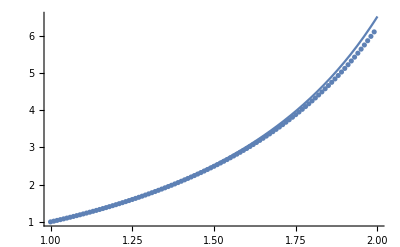

```mathematica
u[x_]:= x/(1-Log[x]);
G1 = Plot[u[x], {x,x0, b}];
G2 = ListPlot[Res];
Show[G1, G2]
```